## Newton’s Law of Cooling

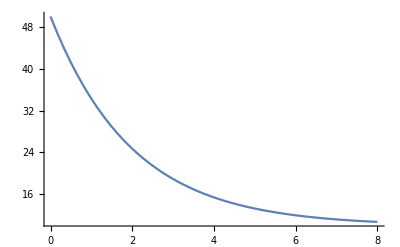

```mathematica
T[t_]:=(T0-Ta)(Exp[-k t])+Ta
params={Ta->10,T0->50,k->0.5};
Plot[T[t]/.params,{t,0,8}]
```

```mathematica
D[T[t],t]
```

-ⅇ^(-k t) k (T0-Ta)

## Dynamic Ambient Temperature

High	78, 3PM
Low	58, 3AM

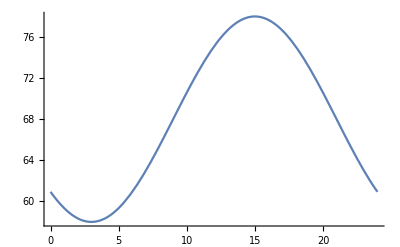

```mathematica
TA[t_]:=1/2(hi-lo)Cos[π/12(t-15)]+1/2(hi+lo)
params={hi->78.,lo->58.,T0->100.,T1->95.,k->0.133787};
Plot[TA[t]/.params,{t,0,24}]
```

Diff Eq:

```mathematica
Tt'[t]==-k(Tt[t]-TA[t])
soln=DSolve[{%,Tt[0]==T0}/.params,Tt[t],t]//First;
T[t_]=Tt[t]/.soln//Simplify
```

Tt'[t]==-k (1/2 (-hi-lo)-1/2 (hi-lo) Cos[1/12 π (-15+t)]+Tt[t])

68.+30.599 ⅇ^(-0.133787 t)+1.40103 Cos[0.261799 t]-4.32948 Sin[0.261799 t]

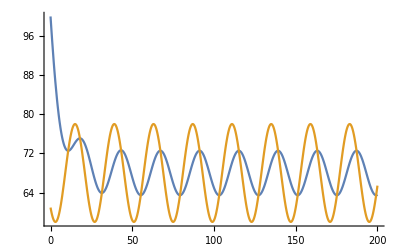

```mathematica
Plot[{T[t],TA[t]/.params},{t,0,200}]
```